# Response Function- Helion 19/02/24

[σ_tot]=μb=10^-4 fm^2
[σ_tot]=mb=10^-1 fm^2
[Lab photon energy] = MeV

```mathematica
dbg=False;
```

#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy,LinearSolve::luc]
Needs["MaTeX`"]
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts}"}];

readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];

trafoToIHeNorm[normMat_]:=Block[{dbg=True},
{evaln,evecn}=Eigensystem[normMat];

diagev=DiagonalMatrix[evaln^(-0.5)];
fulltrafo=Transpose[evecn].diagev;
fulltrafo
];
trafoToIHeNormStab[normMat_,cutoff_:0.0]:=Block[{dbg=True},
{evaln,evecn}=Transpose[Select[Sort[Transpose[Eigensystem[normMat]],#1[[1]]<#2[[1]]&],#[[1]]>cutoff&]];
diagev=DiagonalMatrix[evaln^(-0.5)];
fulltrafo=Transpose[evecn].diagev;
fulltrafo
];
```

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];

parity="-";
Subscript[I, n]={0.5,1.5}; (*Spin of Excited states*)
J0=0.5; (*Spin of Ground states which consists of two channels s and d*)
mIns=Range[-#,#,1]&/@Subscript[I, n];
lege="J_lit="<>ToString[#]&/@Subscript[I, n];
EVthreshold=(10.)^(-8);
dH=1; (* this takes only every dH basis vector into account; ECCE: not benchmarked *)
```

```mathematica
ImgSize=900;
mnucl=938.3;
hbarc=197.3269804; (*codata*)

hbarsqO2m=hbarc^2/(2 mnucl);
(*αfine=1./137.*)
αfine=UnitConvert[Quantity[1,"FineStructureConstant"]];
hat[l_]:=Sqrt[2 l+1];

resultsDir="/home/kirscher/scratch/compton_IRS/MCR/results";

files=FileNames[All,resultsDir];
anzBas=Length[Select[files,StringMatchQ[#,"*mat*BasNR*"]&]]/Length[Subscript[I, n]];

SetDirectory[resultsDir];
dt=ToString[Import["dtype.dat"][[1]][[1]]];
datatype="Real64";
Which[dt=="float32",datatype="Real32",dt=="float64",datatype="Real64"];
Print["Read FORTRAN results from \n",Style[resultsDir,18,Red],"\nin\n",Style[dt,18,Red],"=",Style[datatype,18,Red],"\nformat for\nN_bases=",Style[anzBas,18,Red],"\nevolved bases for the expansion of the final state."];
```

Read FORTRAN results from 
/home/kirscher/scratch/compton_IRS/MCR/results
in
float64=Real64
format for
N_bases=2
evolved bases for the expansion of the final state.

### Read H_nm:=⟨n|(Ĥ)_(V18+UIX)|m⟩ and 𝕟_nm:=⟨n|OverHat[𝟙]|m⟩≠𝟙_nm

```mathematica
HeNormHamMat=readREAL8list["./mat_npp0.5^+"];
tmp=HeNormHamMat[[Range[1,Length[HeNormHamMat],2]]];

HeBasisDimBare=IntegerPart[Sqrt[Length[HeNormHamMat] 0.5]];
Print["bare helion-basis Dimension = ",HeBasisDimBare];

HeNorm=ArrayReshape[HeNormHamMat[[1;;HeBasisDimBare^2]],{HeBasisDimBare,HeBasisDimBare}][[;;;;dH,;;;;dH]];
HeHam=ArrayReshape[HeNormHamMat[[HeBasisDimBare^2+1;;]],{HeBasisDimBare,HeBasisDimBare}][[;;;;dH,;;;;dH]];
```

bare helion-basis Dimension = 2400

transform this basis s.t. one can safely “insert 𝟙”:

```mathematica
fulltrafonm=trafoToIHeNormStab[HeNorm,EVthreshold];
HeNormStab=Transpose[fulltrafonm].HeNorm.fulltrafonm;
HeHamStab=Transpose[fulltrafonm].HeHam.fulltrafonm;
If[False,
Print[ArrayRules[SparseArray[Chop[Transpose[fulltrafonm].HeNorm.fulltrafonm]]]];
Print[fulltrafonm//MatrixForm];
Print[Chop[Transpose[fulltrafonm].HeNorm.fulltrafonm]//MatrixForm];
Print[HeNorm//MatrixForm];];
Print["bare/stabilized initial-state dimension: ",Dimensions[HeNorm],"/",Dimensions[HeNormStab]];
```

bare/stabilized initial-state dimension: {2400,2400}/{1933,1933}

#### The initial state (Helion ground state He )

other parts of this section yield analytic information on the initial state

```mathematica
orderedEVDp=Sort[Transpose[Eigensystem[{HeHamStab,HeNormStab}]],Re[#1[[1]]]<Re[#2[[1]]]&];
evalGSp=orderedEVDp[[1]][[1]];
evecGSp=orderedEVDp[[1]][[2]];
Print["Vector norm of GS (generalized EVP) = ",Norm[evecGSp]];
orderedEVD=Sort[Transpose[Eigensystem[HeHamStab]],Re[#1[[1]]]<Re[#2[[1]]]&];
evalGS=orderedEVD[[1]][[1]];
Print["B(initial) = ",Style[evalGS,Red]," MeV"];
evecGS=orderedEVD[[1]][[2]];
Print["Vector norm of GS (diagonal EVP) = ",Norm[evecGS]];
If[RealDigits[evalGSp,10,6]!=RealDigits[evalGS,10,6],Print["inconsistent GS binding energies!"]]

HeBasisDim=Length[evecGS];
Print["Helion-basis Dimension = ",HeBasisDim];
```

Vector norm of GS (generalized EVP) = 1.

B(initial) = -7.77295 MeV

Vector norm of GS (diagonal EVP) = 1.

Helion-basis Dimension = 1933

### Read H_αβ^J:=⟨α|(Ĥ)_(V18+UIX)|β⟩ and 𝕟_αβ^J:=⟨α|OverHat[𝟙]|β⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the final state, i.e., J^π=(0)^- or J^π=(1)^- or J^π=(2)^- for the negative-parity rank-1 E_1 operator perturbing a Helion;

```mathematica
matnames=FileNames["mat_*^-_BasNR-*"];
matnamesJ=Table[Select[matnames,StringMatchQ[#,"*"<>ToString[Subscript[I, n][[Inn]]]<>"*"]&],{Inn,Range[Length[Subscript[I, n]]]}];

FSNormHamMat=Table[readREAL8list[#]&/@Sort[matnamesJ[[Inn]],ToExpression[StringSplit[#1,"-"][[-1]]]<ToExpression[StringSplit[#2,"-"][[-1]]]&],{Inn,Range[Length[Subscript[I, n]]]}];

FSbasisDim=Table[IntegerPart[Sqrt[Length[#] 0.5]]&/@FSNormHamMat[[Inn]],{Inn,Range[Length[Subscript[I, n]]]}];

Print["Final-state-basis Dimension = ",FSbasisDim];
FSNormBare=Table[ArrayReshape[FSNormHamMat[[Inn]][[#]][[1;;FSbasisDim[[Inn]][[#]]^2]],{FSbasisDim[[Inn]][[#]],FSbasisDim[[Inn]][[#]]}][[;;;;dH,;;;;dH]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];
FSHamBare=Table[ArrayReshape[FSNormHamMat[[Inn]][[#]][[FSbasisDim[[Inn]][[#]]^2+1;;]],{FSbasisDim[[Inn]][[#]],FSbasisDim[[Inn]][[#]]}][[;;;;dH,;;;;dH]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];
```

Final-state-basis Dimension = {{1992,2023},{2166,2119}}

transform this basis s.t. one can safely “insert 𝟙”:

```mathematica
fulltrafosαβ=Table[trafoToIHeNormStab[FSNormBare[[Inn]][[#]],EVthreshold]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];
fulltrafosαβInstab=Table[trafoToIHeNorm[FSNormBare[[Inn]][[#]]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];
Dimensions[fulltrafosαβInstab[[1]][[1]]]
Dimensions[fulltrafosαβ[[1]][[1]]]
Table[Select[ArrayRules[SparseArray[Chop[Transpose[fulltrafosαβ[[nj]][[nb]]].FSNormBare[[nj]][[nb]].fulltrafosαβ[[nj]][[nb]]]]],#[[1]][[1]]!=#[[1]][[2]]&],{nj,Range[Length[Subscript[I, n]]]},{nb,Range[anzBas]}];
FSHam=Table[Transpose[fulltrafosαβ[[nj]][[nb]]].FSHamBare[[nj]][[nb]].fulltrafosαβ[[nj]][[nb]],{nj,Range[Length[Subscript[I, n]]]},{nb,Range[anzBas]}];
FSNorm=Table[Transpose[fulltrafosαβ[[nj]][[nb]]].FSNormBare[[nj]][[nb]].fulltrafosαβ[[nj]][[nb]],{nj,Range[Length[Subscript[I, n]]]},{nb,Range[anzBas]}];
Print["bare/stabilized final-state dimension: ",Dimensions[FSHamBare[[1]][[1]]],"/",Dimensions[FSHam[[1]][[1]]]];
```

{1992,1992}

{1992,1776}

bare/stabilized final-state dimension: {1992,1992}/{1776,1776}

#### The final states

```mathematica
esysFSp=Table[Sort[Transpose[Eigensystem[{FSHam[[Inn]][[Nbb]],FSNorm[[Inn]][[Nbb]]}]],Re[#1[[1]]]<Re[#2[[1]]]&],{Inn,Range[1,Length[Subscript[I, n]]]},{Nbb,Range[anzBas]}];
esysFSp[[1]][[1]][[1;;5,1]]
Norm[esysFSp[[1]][[1]][[1,2]]];
FSDimp=Table[Length[esysFSp[[Inn]][[Nbb]][[1]][[2]]],{Inn,Range[1,Length[Subscript[I, n]]]},{Nbb,Range[anzBas]}]
```

{-2.13403,-2.08534,-2.02417,-1.91889,-1.77386}

{{1776,1797},{2127,2074}}

```mathematica
esysFS=Table[Sort[Transpose[Eigensystem[FSHam[[Inn]][[Nbb]]]],Re[#1[[1]]]<Re[#2[[1]]]&],{Inn,Range[1,Length[Subscript[I, n]]]},{Nbb,Range[anzBas]}];
esysFS[[1]][[1]][[1;;5,1]]
FSDim=Table[Length[esysFS[[Inn]][[Nbb]][[1]][[2]]],{Inn,Range[1,Length[Subscript[I, n]]]},{Nbb,Range[anzBas]}]
Norm[esysFS[[1]][[1]][[1,2]]];
```

{-2.13403,-2.08534,-2.02417,-1.91889,-1.77386}

{{1776,1797},{2127,2074}}

#### Read RHS ⟨α|O_Lm_L|n⟩

the calculation is parallel in n_k parts

```mathematica
CouplingBlockjAs={};

Do[
If[Sign[Subscript[I, n][[nj]]]>=0,JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],2,"0"],JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],3,"0"]];

CouplingBlockjA={};

Do[

CouplingBlock={};
CouplingBlockTA={};

Do[
mM=Select[mLs,ClebschGordan[{multipolarity,#},{J0,mIn-#},{Subscript[I, n][[nj]],mIn}]≠0&];
	(*Why is mM unused here *)
fntmp = "InMIn_"<>ToString[Subscript[I, n][[nj]]]<>"_"<>ToString[mIn]<>"_BasNR-"<>ToString[nb]<>"."<>dt;
tmp =BinaryReadList[fntmp,datatype];

OutDim=Dimensions[tmp][[1]]/HeBasisDimBare;

test=ArrayReshape[tmp,{OutDim,HeBasisDimBare}][[;;;;dH,;;;;dH]];
testy=Table[If[NumberQ[test[[col,row]]],test[[col,row]],0.0],{col,Range[OutDim]},{row,Range[HeBasisDimBare]}];
(*Print[Select[Flatten[testy],Abs[#]>10^3&]];*)

AppendTo[CouplingBlockTA,{mIn,testy}];

,{mIn,mIns[[nj]]}];

AppendTo[CouplingBlockjA,CouplingBlockTA];

,{nb,Range[anzBas]}];

AppendTo[CouplingBlockjAs,CouplingBlockjA];

,{nj,Range[1,Length[Subscript[I, n]]]}];

Print["Dim(⟨ψ|ο̂|D⟩) = ",Table[Dimensions[CouplingBlockjAs[[Inn]][[#]][[1]][[2]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];
Print["Dim(⟨ψ|Ĥ|ψ⟩) = ",Table[Dimensions[FSHam[[Inn]][[#]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];
Print["Dim(⟨ψ|OverHat[1]|ψ⟩) = ",Table[Dimensions[FSNorm[[Inn]][[#]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];
```

Dim(⟨ψ|ο̂|D⟩) = {{{1992,2400},{2023,2400}},{{2166,2400},{2119,2400}}}

Dim(⟨ψ|Ĥ|ψ⟩) = {{{1776,1776},{1797,1797}},{{2127,2127},{2074,2074}}}

Dim(⟨ψ|OverHat[1]|ψ⟩) = {{{1776,1776},{1797,1797}},{{2127,2127},{2074,2074}}}

```mathematica
nj=1;nb=1;nb2=2;
Grid[{{
MatrixPlot[Chop[CouplingBlockjAs[[nj]][[nb]][[1]][[2]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->"finalÔinitial FS basis set "<>ToString[Style[nb,Red],StandardForm],ImageSize->Large],MatrixPlot[Chop[CouplingBlockjAs[[nj]][[nb2]][[1]][[2]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->"finalÔinitial FS basis set "<>ToString[Style[nb2,Red],StandardForm],ImageSize->Large]
},{
MatrixPlot[Chop[FSHam[[nj]][[nb]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->Style["(Ĥ)_setA","Title"],ImageSize->Large]
,
MatrixPlot[Chop[HeHamStab],FrameLabel->{MaTeX["{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{D Hamiltonian}",Magnification->2],ImageSize->Large]
}}]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

#### Analysis of RHS

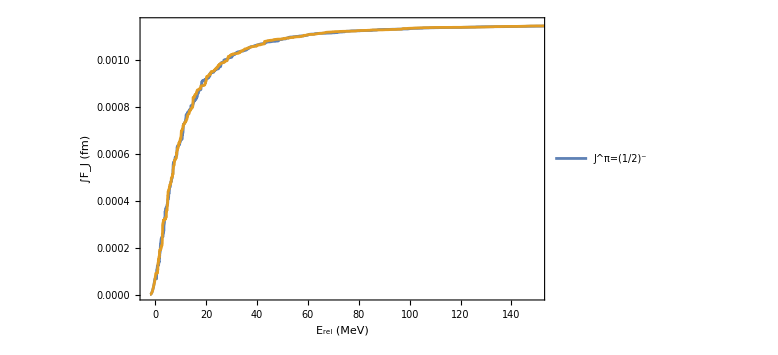
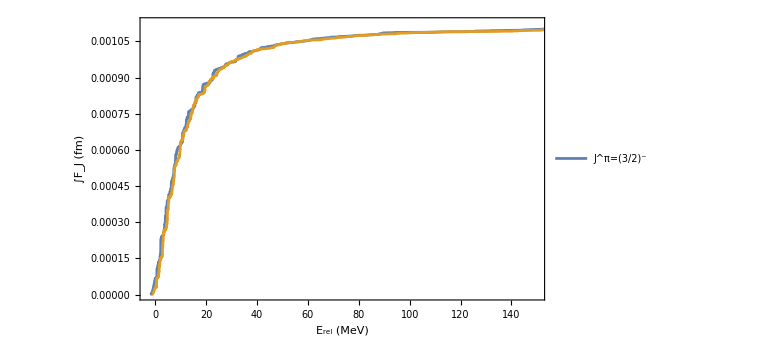
-Graphics- | -Graphics-

```mathematica
maxBas=anzBas;
inhomoEB=Table[{},{nj,Length[Subscript[I, n]]},{nb,Range[maxBas]}];
Do[(* final-state-J loop *)
Do[(* basis-scenario loop *)
Do[(* Subscript[m, L] loop *)
tmpt=Transpose[fulltrafosαβ[[nj]][[nb]]].CouplingBlockjAs[[nj]][[nb]][[mm]][[2]].fulltrafonm;
tmpf=Table[{
esysFS[[nj]][[nb]][[nfs]][[1]],
αfine (esysFS[[nj]][[nb]][[nfs]][[2]].tmpt.evecGS)^2
},{nfs,1,FSDim[[nj]][[nb]]}];

AppendTo[inhomoEB[[nj]][[nb]],tmpf];

,{mm,Range[1,Length[mIns[[nj]]]]}
];
,{nb,Range[maxBas]}
];
,{nj,Range[1,Length[Subscript[I, n]]]}
];
fns=Table[Transpose[{inhomoEB[[Inn]][[nbb]][[1]][[All,1]],Accumulate[inhomoEB[[Inn]][[nbb]][[1]][[All,2]]]}],{Inn,Range[1,Length[Subscript[I, n]]]},{nbb,Range[maxBas]}];
(*fnsp=Table[Transpose[{inhomoEBp[[Inn]][[nbb]][[All,1]],Accumulate[inhomoEBp[[Inn]][[nbb]][[All,2]]]}],{Inn,Range[1,Length[Subscript[I, n]]]},{nbb,Range[maxBas]}];*)
Grid[{{ListPlot[fns[[1]],PlotRange->{{-3,150},All},ImageSize->Large,Frame->True,PlotRangePadding->0,FrameLabel->{"E_rel (MeV)","∫F_J (fm)"},LabelStyle->Large,Joined->True,PlotLegends->{"J^π=(1/2)^-"}],
ListPlot[fns[[2]],PlotRange->{{-3,150},All},ImageSize->Large,Frame->True,PlotRangePadding->0,FrameLabel->{"E_rel (MeV)","∫F_J (fm)"},LabelStyle->Large,Joined->True,PlotLegends->{"J^π=(3/2)^-"}]}}]
```